```mathematica
(* Modeling evaporative flux at unsaturated condition *)
```

```mathematica
(*Experiment data for unsaturated {water table (mm), flux (mm/day), SD flux (mm/day)}*)
(*H = 00 mm *)CS00={{15, 22.8, 1.692368723},{50 ,22.6 ,2.56},{60 ,22.3 ,1.655665703},{100 ,18.7 ,0.935776814},{140, 15.83550764 ,0.032173191},{185, 1.7,0.1}};
(*H = 05 mm *)CS05={{15 ,8.432803188 ,0.952999281},{50,8.294272084, 1.373242726},{100 ,7.924590886 ,0.93612619},{140, 9.132759353 ,1.23586792},{185 ,3.72 ,2.09}};
(*H = 10 mm *)CS10={{15, 6.814120392, 1.123055292},{50, 6.486910315, 1.14901281},{100, 5.574764303 ,0.915018004},{140 ,5.84271247 ,1.526689857},{185 ,2.03 ,1.29}};
```

Best-fit parameter: {lambda→0.368028}

Fitted equation: 22.8/(1+0.368028 H)

| Estimate | Standard Error | t-Statistic | P-Value
lambda | 0.368028 | 0.0172877 | 21.2884 | 4.24008×10^-6

Weighted sum of squared residuals: 3.32595

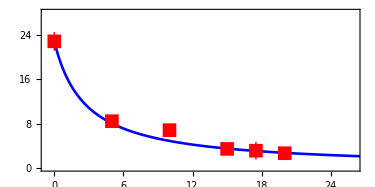

```mathematica
ClearAll[H,lambda,J0,data,xy,weights,fit,chiSquared,dataPlot,modelPlot];

(*Columns:mulch thickness (mm),flux (mm/day),uncertainty*)
data={{0,22.8,1.69},{5,8.43,0.953},{10,6.81,1.123},{15,3.438,0.149399},{17.5,3.11333,1.59193},{20,2.66,0.59397}};

J0=22.8;
xy=data[[All,{1,2}]];
weights=1/data[[All,3]]^2;

(*Fit lambda*)
JwetM=NonlinearModelFit[xy,{J0/(1+lambda H),lambda>0},{{lambda,1}},H,Weights->weights,VarianceEstimatorFunction->(1&)];

Print["Best-fit parameter: ",JwetM["BestFitParameters"]];
Print["Fitted equation: ",Normal[JwetM]];
Quiet[Print[JwetM["ParameterTable"]]];

chiSquared=Total[weights JwetM["FitResiduals"]^2];
Print["Weighted sum of squared residuals: ",chiSquared];

(*Plot experimental data with error bars*)
dataPlot=Table[{data[[i,1]],Around[data[[i,2]],data[[i,3]]]},{i,1,6}];

Show[{
Plot[JwetM[H],{H,0,28},PlotStyle->Directive[Blue,Thickness[0.005]],PlotRange->{{-0.6,26},{0,28}},Frame->True,AspectRatio->1.5/3,ImageSize->{375,200},FrameStyle->Directive[{15,Black,Thickness[0.003]}]],
ListPlot[dataPlot,PlotStyle->Red,PlotMarkers->{"■",14}]
}]
```

```mathematica
ClearAll[Jw,Jd,a,b]
```

```mathematica
Jw[H_]:=22.8/(1+0.368 H);
Jd[H_,wt_]:=22.8/(1+0.368 (wt+H));
```

```mathematica
(*1. Define the dataset:{x,y}*)
data=Table[{CS00[[i,1]],CS00[[i,2]]},{i,1,Length[CS00]}];

(*2. Define the model function*)
model[x_,a_,b_]:=(1/2×(1-Tanh[(x-a)/b]))Jw[0]+(1-1/2×(1-Tanh[(x-a)/b]))Jd[0,x];

(*---NonlinearModelFit---*)
nlm=NonlinearModelFit[data,{model[x,a,b],a>0,b>0},{{a,150},{b,30}},x];

(*Display summary table containing Best-Fit Values,Standard Errors,t-Statistics,and p-Values*)
Print["=== NonlinearModelFit Parameter Summary ==="];
Quiet[nlm["ParameterTable"]]

(*Extract specific properties*)
Print["Best Fit Parameters: ",Quiet[nlm["BestFitParameters"]]];
Print["Standard Errors:     ",Quiet[nlm["ParameterErrors"]]];
Print["Residual SS (RSS):   ",Quiet[nlm["EstimatedVariance"]]*(Length[data]-2)];
```

=== NonlinearModelFit Parameter Summary ===

| Estimate | Standard Error | t-Statistic | P-Value
a | 149.597 | 5.24611 | 28.5157 | 9.00038×10^-6
b | 35.4996 | 9.43066 | 3.76428 | 0.0197017

Best Fit Parameters: {a→149.597,b→35.4996}

Standard Errors:     {5.24611,9.43066}

Residual SS (RSS):   11.4519

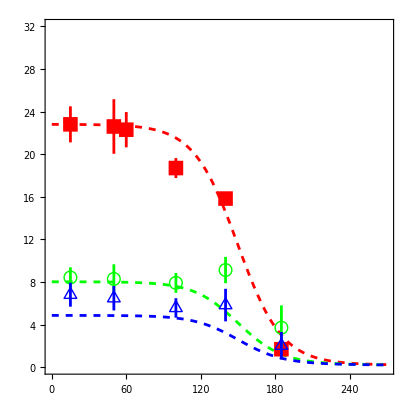

```mathematica
(* Obtaining Fig 7a *)
a=149.597;
b=35.4996;
Show[{
Plot[{
(1/2×(1-Tanh[(wt-a)/b]))Jw[0]+(1-1/2×(1-Tanh[(wt-a)/b]))Jd[0,wt],
(1/2×(1-Tanh[(wt-a)/b]))Jw[5]+(1-1/2×(1-Tanh[(wt-a)/b]))Jd[5,wt],
(1/2×(1-Tanh[(wt-a)/b]))Jw[10]+(1-1/2×(1-Tanh[(wt-a)/b]))Jd[10,wt]
},{wt,0, 270},PlotRange->{{0,270},{0.,32}},PlotStyle->{{Dashed,Red},{Dashed,Green},{Dashed,Blue}}],
ListPlot[Table[{CS00[[i,1]],CS00[[i,2]]},{i,1,Length[CS00]}],Joined->False,PlotStyle->Red,PlotMarkers->{"■",15},PlotRange->{{0,270},{0,25}}],
ListPlot[Table[{{CS00[[i,1]],CS00[[i,2]]-CS00[[i,3]]},{CS00[[i,1]],CS00[[i,2]]+CS00[[i,3]]}},{i,1,Length[CS00]}],Joined->True,PlotStyle->Red],
ListPlot[Table[{CS05[[i,1]],CS05[[i,2]]},{i,1,Length[CS05]}],Joined->False,PlotStyle->Green,PlotMarkers->{"○",13},PlotRange->{{0,270},{0,25}}],
ListPlot[Table[{{CS05[[i,1]],CS05[[i,2]]-CS05[[i,3]]},{CS05[[i,1]],CS05[[i,2]]+CS05[[i,3]]}},{i,1,Length[CS05]}],Joined->True,PlotStyle->Green],
ListPlot[Table[{CS10[[i,1]],CS10[[i,2]]},{i,1,Length[CS10]}],Joined->False,PlotStyle->Blue,PlotMarkers->{"△",15},PlotRange->{{0,270},{0,25}}],
ListPlot[Table[{{CS10[[i,1]],CS10[[i,2]]-CS10[[i,3]]},{CS10[[i,1]],CS10[[i,2]]+CS10[[i,3]]}},{i,1,Length[CS10]}],Joined->True,PlotStyle->Blue]
},Frame->True,AspectRatio->1,ImageSize->{205,200}*2,FrameStyle->Directive[{15,Black,Thickness[0.00275]}]]
```

```mathematica
(*Sensitivity analysis*)
(*Given values and uncertainties*)
bMean=b;
bErr=9.43066;
lcMean=81.0;
lcErr=1.0; 

(*Calculate nominal lp *)
lpNominal=2*Pi*bMean-lcMean;

(*Propagated standard error for lp*)
lpErr=Sqrt[(2*Pi*bErr)^2+(-1*lcErr)^2];

Print["lp + lc (mm):",2*Pi*bMean];
Print["Nominal lp (mm): ",lpNominal];
Print["Propagated Error sigma_lp (mm): ",lpErr];
Print["Range for lp: ",lpNominal-lpErr," to ",lpNominal+lpErr," mm"];
```

lp + lc (mm):223.051

Nominal lp (mm): 142.051

Propagated Error sigma_lp (mm): 59.263

Range for lp: 82.7875 to 201.314 mm

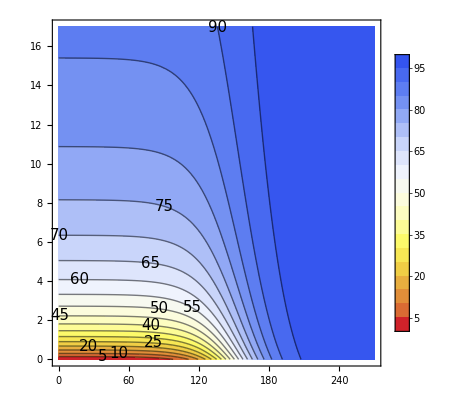

```mathematica
(* Obtaining Fig 7b *)
(* Equation 12 *)
func[wt_,H_]:=(1/2×(1-Tanh[(wt-a)/b]))Jw[H]+(1-1/2×(1-Tanh[(wt-a)/b]))Jd[H,wt];
ContourPlot[(func[0,0]-func[wt,H])/func[0,0] 100,{wt,0,270},{H,0,17},MaxRecursion->4,PerformanceGoal->"Quality",Contours->Range[5,100,5],ColorFunction->ColorData[{"TemperatureMap","Reverse"}],Frame->True,AspectRatio->1,ImageSize->{200,200}*2,FrameStyle->Directive[{15,Black,Thickness[0.00275]}],ContourLabels->(If[Abs[#2-(17/200) #1]<8,Text[Style[#3,15,Black,Background->None],{#1,#2}]]&),PlotLegends->BarLegend[Automatic,LegendLabel->Style[" ",15,Black],LabelStyle->{15,Black},LegendMarkerSize->375]]
```